# 本征值

```mathematica
Clear["Global`*"]
```

## 公式

```mathematica
hh=({{0, -2.97*(Exp[I*(Sqrt[3]*kx/2-ky/2)]+Exp[I*ky]+Exp[I*(-Sqrt[3]*kx/2-ky/2)]), 0, -0.33}, {-2.97*(Exp[-I*(Sqrt[3]*kx/2-ky/2)]+Exp[-I*ky]+Exp[-I*(-Sqrt[3]*kx/2-ky/2)]), 0, 0, 0}, {0, 0, 0, -2.97*(Exp[I*(Sqrt[3]*kx/2-ky/2)]+Exp[I*ky]+Exp[I*(-Sqrt[3]*kx/2-ky/2)])}, {-0.33, 0, -2.97*(Exp[-I*(Sqrt[3]*kx/2-ky/2)]+Exp[-I*ky]+Exp[-I*(-Sqrt[3]*kx/2-ky/2)]), 0}})
```

{{0,-2.97 (ⅇ^(ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(ⅈ ((√3 kx)/2-ky/2))+ⅇ^(ⅈ ky)),0,-0.33},{-2.97 (ⅇ^(-ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(-ⅈ ((√3 kx)/2-ky/2))+ⅇ^(-ⅈ ky)),0,0,0},{0,0,0,-2.97 (ⅇ^(ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(ⅈ ((√3 kx)/2-ky/2))+ⅇ^(ⅈ ky))},{-0.33,0,-2.97 (ⅇ^(-ⅈ (-(√3 kx)/2-ky/2))+ⅇ^(-ⅈ ((√3 kx)/2-ky/2))+ⅇ^(-ⅈ ky)),0}}

## 定义将分段直线化为参数方程的函数

```mathematica
F={0,0,0};
M=Pi/a {1,1/Sqrt[3],0};
K=4Pi/a {1/3,0,0};
```

## 作图

```mathematica
fun[t_]:=Piecewise[{{{t,0,0},0<=t<(4 π)/(3 √3)},{{(4 π)/(3 √3)+1/2 (-t+(4 π)/(3 √3)),1/2 √3 (t-(4 π)/(3 √3)),0},(4 π)/(3 √3)<=t<(2 π)/(√3)},{{π/(√3)-1/2 √3 (t-(2 π)/(√3)),π/3+1/2 (-t+(2 π)/(√3)),0},(2 π)/(√3)<=t<(2 π)/3+(2 π)/(√3)}},{0,0,0}]
```

```mathematica
fun[j]
```

Piecewise[{{{j,0,0}, 0≤j<(4 π)/(3 √3)}, {{(4 π)/(3 √3)+1/2 (-j+(4 π)/(3 √3)),1/2 √3 (j-(4 π)/(3 √3)),0}, (4 π)/(3 √3)≤j<(2 π)/(√3)}, {{π/(√3)-1/2 √3 (j-(2 π)/(√3)),π/3+1/2 (-j+(2 π)/(√3)),0}, (2 π)/(√3)≤j<(2 π)/3+(2 π)/(√3)}, {{0,0,0}, True}}]

```mathematica
RegionMeasure[Line[{F,K,M,F}]]/.{a->Sqrt[3]}//N
```

5.72199

```mathematica
ParametricPlot3D[{fun[t][[1]],fun[t][[2]],fun[t][[3]]},{t,0,5.72199}]
```

-Graphics3D-

```mathematica
table=Table[{ba,Eigenvalues[hh/.{kx->fun[ba][[1]],ky->fun[ba][[2]]}]},{ba,0.0000000000000001,5.721993830861631,0.001}];
```

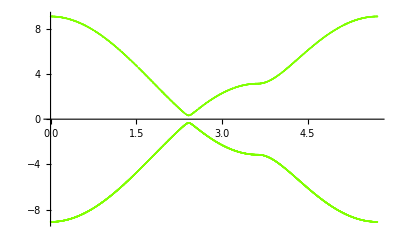
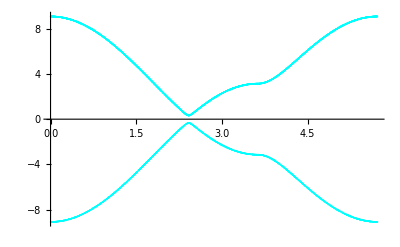
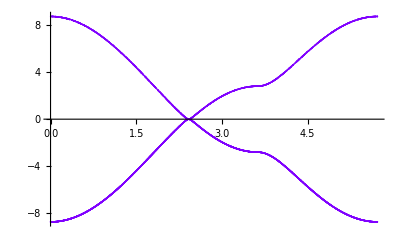
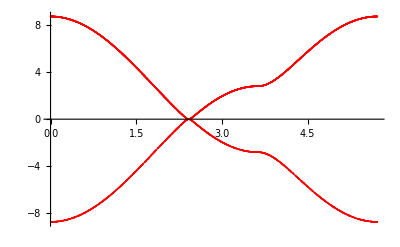

```mathematica
Table[ListPlot[Riffle[table[[All,1]],table[[All,2,i]]]//Partition[#,2]&,PlotRange->All,PlotStyle->Hue[i/Dimensions[hh][[1]]]],{i,1,Dimensions[hh][[1]]}]
```

```mathematica
part={ , , , }
```

{Null,Null,Null,Null}

```mathematica
part[[1]]=Riffle[table[[All,1]],Abs@table[[All,2,1]]];
```

```mathematica
part[[2]]=Riffle[table[[All,1]],-Abs@table[[All,2,1]]];
```

```mathematica
part[[3]]=Riffle[table[[All,1]],Abs@table[[All,2,3]]];
```

```mathematica
part[[4]]=Riffle[table[[All,1]],-Abs@table[[All,2,3]]];
```

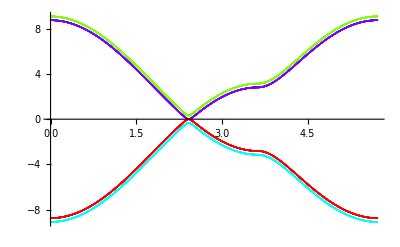

```mathematica
Table[ListPlot[part[[i]]//Partition[#,2]&,PlotRange->All,PlotStyle->Hue[i/4]],{i,1,4}]//Show[#,PlotRange->All]&
```